```mathematica
Clear["Global`*"];
Needs["VectorAnalysis`"];
```

```mathematica
Geometry={Disk[],Rectangle[{1,2},{7,4}],Triangle[{{3,0},{6,1},{2,-1.5}}]};
Graphics[Geometry];
DiscretizeRegion[RegionDifference[Rectangle[{-3,-3},{9,6}],RegionUnion@@Geometry]];
HighlightMesh[bMesh=BoundaryMesh[DiscretizeRegion[RegionUnion@@Geometry]],Labeled[0,"Index"]]
NEl=MeshCellCount[%,1];
```

-Graphics-

```mathematica
BElts=MeshPrimitives[bMesh,1];
Knots=RegionCentroid/@BElts;
```

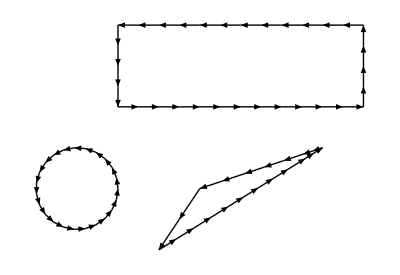

```mathematica
Graphics[{Arrowheads[.02],Table[Arrow[{BElts[[i,1,1]],BElts[[i,1,2]]}],{i,1,NEl}]}]
```

```mathematica
TriangleInd=  Select[Range[NEl],6≥ Knots[[#,1]]≥ 2 && -1.5≤ Knots[[#,2]]≤1 &];
RectangleInd = Select[Range[NEl],Knots[[#,1]]≥ 0.9 && 1.5≤ Knots[[#,2]]≤4.5 &];
DiskInd = Select[Range[NEl],Knots[[#,1]]≤1 && Knots[[#,2]]≤1 &];
```

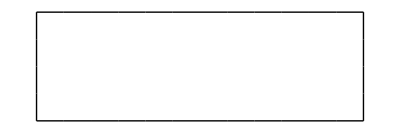
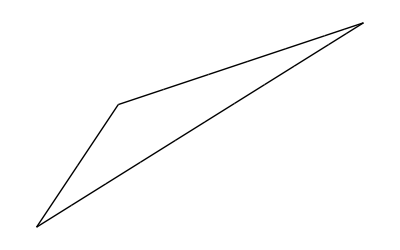
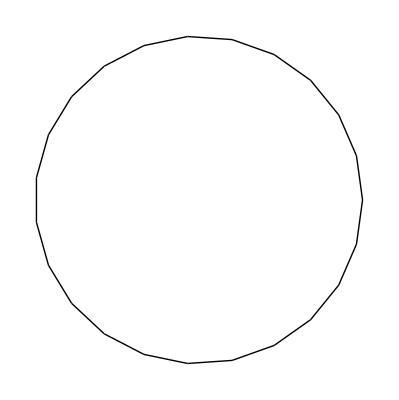

```mathematica
{Graphics[BElts[[RectangleInd]]],
Graphics[BElts[[TriangleInd]]],
Graphics[BElts[[DiskInd]]]}
```

```mathematica
Startings=ParallelTable[BElts[[i,1,1]],{i,1,NEl}];
CountAmmount =ParallelTable[Count[BElts[[All,1,1]],BElts[[i,1,1]]],{i,1,NEl}];
Length[CountAmmount]==Count[CountAmmount,1]
```

True

```mathematica
Finishings=ParallelTable[BElts[[i,1,2]],{i,1,NEl}];
CountAmmount =ParallelTable[Count[BElts[[All,1,2]],BElts[[i,1,2]]],{i,1,NEl}];
Length[CountAmmount]==Count[CountAmmount,1]
```

True

```mathematica
RectangleCenter = {4,3};
V1CrossProduct=ParallelTable[
CrossProduct[
Append[BElts[[i,1,1]]-RectangleCenter,0],
Append[BElts[[i,1,2]]-RectangleCenter,0]
],{i,Min[RectangleInd],Max[RectangleInd]}];
V1CrossProduct=ParallelTable[V1CrossProduct[[i,3]],{i,1,Length[V1CrossProduct]}];
V1CrossProduct=ParallelTable[Sign[V1CrossProduct[[i]]],{i,1,Length[V1CrossProduct]}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
TriangleCenter =({3,0}+{6,1}+{2,-1.5})/3;
V2CrossProduct=ParallelTable[
CrossProduct[
Append[BElts[[i,1,1]]-TriangleCenter,0],
Append[BElts[[i,1,2]]-TriangleCenter,0]
],{i,Min[TriangleInd],Max[TriangleInd]}];
V2CrossProduct=ParallelTable[V2CrossProduct[[i,3]],{i,1,Length[V2CrossProduct]}];
V2CrossProduct=ParallelTable[Sign[V2CrossProduct[[i]]],{i,1,Length[V2CrossProduct]}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
CircleCenter = {0,0};
V3CrossProduct=ParallelTable[
CrossProduct[
Append[BElts[[i,1,1]]-CircleCenter,0],
Append[BElts[[i,1,2]]-CircleCenter,0]
],{i,Min[DiskInd],Max[DiskInd]}];
V3CrossProduct=ParallelTable[V3CrossProduct[[i,3]],{i,1,Length[V3CrossProduct]}];
V3CrossProduct=ParallelTable[Sign[V3CrossProduct[[i]]],{i,1,Length[V3CrossProduct]}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}